```mathematica
<<MaTeX`
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{newtxmath}"}];
```

```mathematica
ConfigureMaTeX["pdfLaTeX"->"/Library/TeX/texbin/pdflatex","Ghostscript"->"/usr/local/bin/gs"];
```

```mathematica
texStyle2={FontFamily->"Latin Modern Roman",FontSize->12};
```

```mathematica
hCons=6.62607015*10^-34;
```

```mathematica
Cvel=299792458;
```

```mathematica
LambdaLaser=852*10^-9;
```

```mathematica
Φ[P_]:=(P*LambdaLaser)/(hCons*Cvel)
```

```mathematica
npro[η_,Φ_,T_]:=η*Φ*T;
```

```mathematica
EtaM[npromM_,P_,T_]:=npromM/npro[1,Φ[P],T]
```

```mathematica
PoissonDis[n_,η_,P_,T_]:=npro[η,Φ[P],T]^n/(n!)ⅇ^(-npro[η,Φ[P],T])
```

```mathematica
OP[IP_,OD_]:=IP*10^-OD;
```

```mathematica
OD[IP_,OP_]:=Log[10,IP/OP]
```

```mathematica
L1[aa_,bb_,Dellta_,Amp2_]:=Table[If[i≤ 1*10^-7&&i≥ -1*10^-7,{0,MaTeX[0,Magnification->Amp2]},{i,MaTeX[i,Magnification->Amp2]}],{i,aa,bb,Dellta}]
```

```mathematica
L2[aa_,bb_,Dellta_,Tc1_,Tc2_]:=Table[If[Mod[i,2]==0, If[aa+(Dellta*i)==0,{0,Directive[Black,Thickness[Tc1]]},{aa+(Dellta*i),Directive[Black,Thickness[Tc1]]}], If[aa+(Dellta*i)==0,{0,Directive[Black,Thickness[Tc2],Dashed]},{aa+(Dellta*i),Directive[Black,Thickness[Tc2],Dashed]}]],{i,0,(bb-aa)/Dellta,1}]
```

```mathematica
T4[P_,DeltaX_,Delt_,Xmin_,Xmax_,T_]:=Table[Insert[Insert[Table[{j,PoissonDis[i,0.56,P,T]},{j,i-DeltaX,i+DeltaX,DeltaX*Delt}],{i+DeltaX,0},IntegerPart[2/Delt]+2],{i-DeltaX,0},1],{i,Xmin,Xmax}]
```

```mathematica
L22[p_,T_,a_,Xmin_,Xmax_,DeltaXMin_,Tc1_,Tc2_]:=ListLinePlot[T4[p,0.3,0.1,Xmin,Xmax,T],Axes->True,PlotRange->{{Xmin-0.5,Xmax},{0,1}},Ticks->{Table[i,{i,Xmin-1,Xmax+1,1}],Table[i,{i,0,1,0.1}]},FrameTicks->{{L1[0,1,0.2,a],Automatic},{L1[Xmin,Xmax,DeltaXMin,a],Automatic}},AspectRatio->2/3,Filling->Axis,PlotStyle->Red,Frame->True,GridLines->{L2[Xmin,Xmax,DeltaXMin*0.5,Tc1,Tc2],L2[0,1,0.05,Tc1,Tc2]},FrameLabel->{Text[MaTeX["n",Magnification->1.2]],Text[MaTeX["\\mathcal{P}_{\\rm{T}}(n)",Magnification->1.2]]}]
```

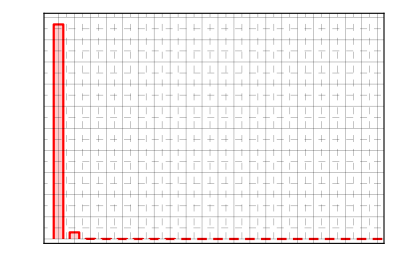

0.030744

```mathematica
(*p=0.1pW*)
L22[10^-13,128*10^-9,0.9,0,20,1,0.001,0.001]
npro[0.56,Φ[10^-13],128*10^-9]
```

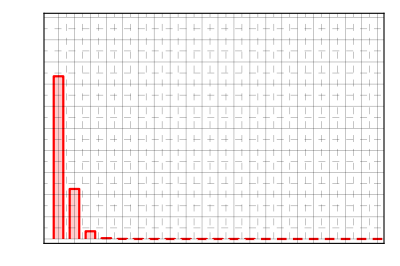

0.30744

```mathematica
(*p=1pW*)
L22[10^-12,128*10^-9,0.9,0,20,1,0.001,0.001]
npro[0.56,Φ[10^-12],128*10^-9]
```

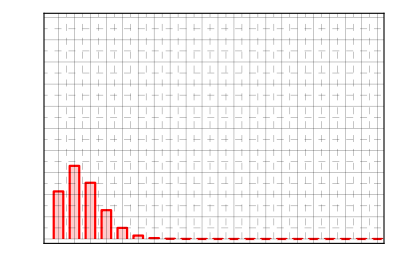

1.5372

```mathematica
(*p=5pW*)
L22[5*10^-12,128*10^-9,0.9,0,20,1,0.001,0.001]
npro[0.56,Φ[5*10^-12],128*10^-9]
```

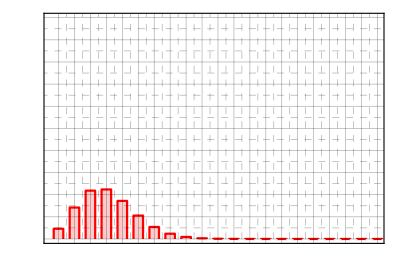

3.0744

```mathematica
(*p=10pW*)
L22[10*10^-12,128*10^-9,0.9,0,20,1,0.001,0.001]
npro[0.56,Φ[10*10^-12],128*10^-9]
```

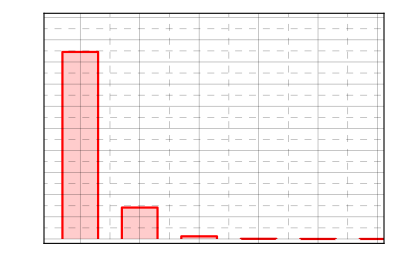

0.3

```mathematica
(*p=0.136612pW*)
L22[1.36612*10^-13,512*10^-9,0.9,0,5,1,0.001,0.001]
npro[1,Φ[1.36612*10^-13],512*10^-9]
```